```mathematica
ClearAll@genPoints;
ClearAll@approximation;
genPoints[x0_,x1_,f_,n_]:=Module[{x,y,h},

x=Table[x0+i*(x1-x0)/(n-1),{i,n}];
y=Table[f[x[[i]]],{i,n}];
{x,y}
]
approximation[f_]:=Module[{ϕ,r,a},
ϕ={
(1/Sqrt[Pi])&,
(#*Sqrt[2/Pi])&,
((2*#^2-1)*Sqrt[2/Pi])&,
((4#^3-3#)*Sqrt[2/Pi])&,
((8#^4-8#^2+1)*Sqrt[2/Pi])&,
((16#^5-20#^3+5#)*Sqrt[2/Pi])&
};
r=(1/(1-#^2))^(1/2)&;
a=Table[NIntegrate[r[u]f[u]ϕi[u],{u,-1,1}],{ϕi,ϕ}];
(Sum[a[[i]] ϕ[[i]][#],{i,Length@a}])&
]
```

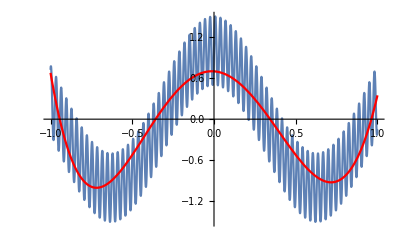

```mathematica
f1[x_]:=Cos[5x]+0.5Sin[200x];
res1=approximation[f1];
Show[
Plot[f1[x],{x,-1,1}],
Plot[res1[x],{x,-1,1},PlotStyle->Red]
]
```

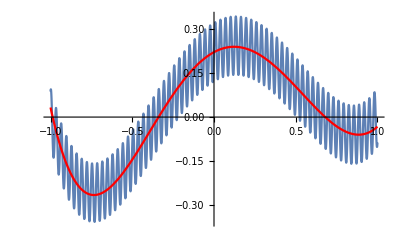

```mathematica
f2[x_]:=(x-1)(x+1)(x-2/3)(x+1/3)+0.1Sin[200x];
res1=approximation[f2];
Show[
Plot[f2[x],{x,-1,1}],
Plot[res1[x],{x,-1,1},PlotStyle->Red]
]
```

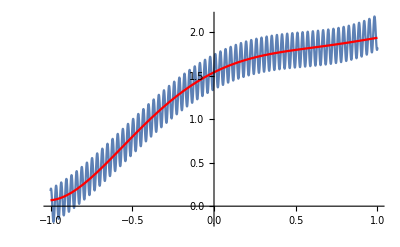

```mathematica
f3[x_]:=Cosh[-x^2+1]+x+0.2Sin[200x];
res1=approximation[f3];
Show[
Plot[f3[x],{x,-1,1}],
Plot[res1[x],{x,-1,1},PlotStyle->Red]
]
```

```mathematica
f1[x_]:=Cos[5x]+0.5Sin[200x];
f2[x_]:=(x-1)(x+1)(x-2/3)(x+1/3)+0.1Sin[200x];
f3[x_]:=Cosh[-x^2+1]+x+0.2Sin[200x];
```